```mathematica
Clear["Global`*"];
```

### Plot settings

```mathematica
Import[NotebookDirectory[] <>"/tools/LogScale.m"];
Import[NotebookDirectory[] <>"/tools/LogTicks.m"];
Import[NotebookDirectory[] <>"/tools/MyGrid.m"];
Import[NotebookDirectory[] <>"/tools/KPTools.m"];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
ticksx=LogTicks[-15, -2,2];
ticksy=LogTicks[0,2,1];
ticksx0=LogTicksNoLabel[-14,-2];
ticksy0=LogTicksNoLabel[0,2];
ticksy=Join[ {{0.,"1"},{1.,"10"},{2.,"100"}},LogTicksNoLabel[0,2]];
fticksx=Join[{{-3.,"0.001"},{-2.,"0.01"},{-1.,"0.1"},{0.,"1"},{1.,"10"},{2.,"100"}},LogTicks[-10,-4,2],LogTicksNoLabel[-4,4]];
fticksy=Join[{{-2.,"0.01"},{0.,"1"},{2.,"100"}},LogTicks[-14,-4,2],LogTicksNoLabel[-4,4]];
fticksx0=LogTicksNoLabel[-10,4];
fticksy0=LogTicksNoLabel[-14,4];
lticksy=Join[{{-2.,"0.01"},{-1.,"0.1"},{0.,"1"}},LogTicks[-14,-4,2],LogTicksNoLabel[-4,4]];
```

```mathematica
barlegend=BarLegend[{Blend[{{0,Hue[0.,0.1,1]},{1,Hue[0.,1,1]},{1.01,Hue[0.3,0.1,1]},{2,Hue[0.3,1,1]},{2.01,Hue[0.7,0.1,1]},{3,Hue[0.7,1,1]}},#]&,{0,3}},"Ticks"->{0,1,2,3},"TickLabels"->{"0.1","1","10","100"},LegendLabel->Style[HoldForm["ϵ_P"],20,Black,FontFamily->"Times"],LabelStyle->{FontFamily->"Times",FontSize->20},LegendLayout->"Column",ColorFunctionScaling->False];
```

### Experimental sensitivities

#### KATRIN

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
KATRINdata=Import[NotebookDirectory[]<>"/exp_sensitivity/KATRINXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
KATRINres= Table[{KATRINdata⟦i,1⟧,KATRINdata⟦i,2⟧*4} ,{i,1,Length[KATRINdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
KATRINtr=Transpose[{Table[KATRINres⟦i,2⟧,{i,1,Length[KATRINres]}],Table[KATRINres⟦i,1⟧,{i,1,Length[KATRINres]}]}];
```

```mathematica
KATRIN= Join[{{10^3,First[KATRINtr]⟦2⟧}},KATRINtr,{{10^3,Last[KATRINtr]⟦2⟧}}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
KATLog = Table[{Log10[KATRIN⟦i,1⟧], Log10[KATRIN⟦i,2⟧]}, {i ,1,Length[KATRIN]}];
```

#### TRISTAN

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
TRISTANdata=Import[NotebookDirectory[]<>"/exp_sensitivity/TRISTANXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
TRISTANres= Table[{TRISTANdata⟦i,1⟧,TRISTANdata⟦i,2⟧*4} ,{i,1,Length[TRISTANdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
TRISTANtr=Transpose[{Table[TRISTANres⟦i,2⟧,{i,1,Length[TRISTANres]}],Table[TRISTANres⟦i,1⟧,{i,1,Length[TRISTANres]}]}];
```

```mathematica
TRISTAN= Join[{{10^3,First[TRISTANtr]⟦2⟧}},TRISTANtr,{{10^3,Last[TRISTANtr]⟦2⟧}}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
TRILog = Table[{Log10[TRISTAN⟦i,1⟧], Log10[TRISTAN⟦i,2⟧]}, {i ,1,Length[TRISTAN]}];
```

#### TRISTAN statistical

taken from "A novel detector system for KATRIN to search for keV-scale sterile neutrinos" [arXiv:physics.ins-det/1810.06711]
x-axis:  m_s , non-log scale, [keV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
TRISTANstatdata=Import[NotebookDirectory[]<>"/exp_sensitivity/TRISTANstatXakeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
TRISTANstatres= Table[{TRISTANstatdata⟦i,1⟧,TRISTANstatdata⟦i,2⟧*4} ,{i,1,Length[TRISTANstatdata]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
TRISTANstattr=Transpose[{Table[TRISTANstatres⟦i,2⟧,{i,1,Length[TRISTANstatres]}],Table[TRISTANstatres⟦i,1⟧,{i,1,Length[TRISTANstatres]}]}];
```

```mathematica
TRISTANstat= Join[{{10^3,First[TRISTANstattr]⟦2⟧}},TRISTANstattr,{{10^3,Last[TRISTANstattr]⟦2⟧}}];
```

```mathematica
ListLogLogPlot[{KATRIN, TRISTAN, TRISTANstat}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
TRIstatLog = Table[{Log10[TRISTANstat⟦i,1⟧], Log10[TRISTANstat⟦i,2⟧]}, {i ,1,Length[TRISTANstat]}];
```

#### ECHo

taken from "A White Paper on keV Sterile Neutrino Dark Matter" [arXiv:1602.04816v1]
x-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4
y-axis:  m_s , non-log scale, [GeV]

```mathematica
ECHodata=Import[NotebookDirectory[]<>"/exp_sensitivity/ECHoYaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ)*)
ECHores= Table[{ECHodata⟦i,1⟧*4,ECHodata⟦i,2⟧} ,{i,1,Length[ECHodata]}];
```

```mathematica
(*the data are now in the plane (sin^2(2θ), Subscript[m, s])*)
```

```mathematica
ECHo= Join[{{10^3,First[ECHores]⟦2⟧}},ECHores,{{10^3,Last[ECHores]⟦2⟧}}];
```

```mathematica
(*rescale to bring the data in keV instead of GeV*)
ECHor = Table[{ECHo⟦i,1⟧,ECHo⟦i,2⟧*10^6} ,{i,1,Length[ECHo]}];
```

```mathematica
ListLogLogPlot[ECHor];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
ECHoLog =  Table[{Log10[ECHor⟦i,1⟧], Log10[ECHor⟦i,2⟧]}, {i ,1,Length[ECHor]}];
```

#### HUNTER phase 1

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER1data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp1XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER1res= Table[{HUNTER1data⟦i,1⟧,HUNTER1data⟦i,2⟧*4} ,{i,1,Length[HUNTER1data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER1tr=Transpose[{Table[HUNTER1res⟦i,2⟧,{i,1,Length[HUNTER1res]}],Table[HUNTER1res⟦i,1⟧,{i,1,Length[HUNTER1res]}]}];
```

```mathematica
HUNTER1= Join[{{10^3,First[HUNTER1tr]⟦2⟧}},HUNTER1tr,{{10^3,Last[HUNTER1tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)
HUNTER1r = Table[{HUNTER1⟦i,1⟧,HUNTER1⟦i,2⟧*10^6} ,{i,1,Length[HUNTER1]}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNT1Log = Table[{Log10[HUNTER1r⟦i,1⟧], Log10[HUNTER1r⟦i,2⟧]}, {i ,1,Length[HUNTER1r]}];
```

#### HUNTER phase 2

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER2data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp2XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER2res= Table[{HUNTER2data⟦i,1⟧,HUNTER2data⟦i,2⟧*4} ,{i,1,Length[HUNTER2data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER2tr=Transpose[{Table[HUNTER2res⟦i,2⟧,{i,1,Length[HUNTER2res]}],Table[HUNTER2res⟦i,1⟧,{i,1,Length[HUNTER2res]}]}];
```

```mathematica
HUNTER2= Join[{{10^3,First[HUNTER2tr]⟦2⟧}},HUNTER2tr,{{10^3,Last[HUNTER2tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)
HUNTER2r = Table[{HUNTER2⟦i,1⟧,HUNTER2⟦i,2⟧*10^6} ,{i,1,Length[HUNTER2]}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNT2Log = Table[{Log10[HUNTER2r⟦i,1⟧], Log10[HUNTER2r⟦i,2⟧]}, {i ,1,Length[HUNTER2r]}];
```

#### HUNTER phase 3

taken from "Design of  the electron spectrometer for the HUNTER experiment" [thesis by Francesco Granato]
x-axis:  m_s , log scale, [GeV]
y-axis:  sin^2(θ), log scale, -> if we want to plot sin^2(2θ), we must multiply the data we have by a factor of 4

```mathematica
HUNTER3data=Import[NotebookDirectory[]<>"/exp_sensitivity/HUNTERp3XaGeV.dat"];
```

```mathematica
(*rescaled data to get sin^2(2θ) from sin^2(θ), (Subscript[m, s], sin^2(2θ))*)
HUNTER3res= Table[{HUNTER3data⟦i,1⟧,HUNTER3data⟦i,2⟧*4} ,{i,1,Length[HUNTER3data]}];
```

```mathematica
(*contains the rescaled transposed data, in the plane (sin^2(2θ), Subscript[m, s])*)
HUNTER3tr=Transpose[{Table[HUNTER3res⟦i,2⟧,{i,1,Length[HUNTER3res]}],Table[HUNTER3res⟦i,1⟧,{i,1,Length[HUNTER3res]}]}];
```

```mathematica
HUNTER3= Join[{{10^3,First[HUNTER3tr]⟦2⟧}},HUNTER3tr,{{10^3,Last[HUNTER3tr]⟦2⟧}}];
```

```mathematica
(*to bring the mass data in keV (from GeV)*)HUNTER3r = Table[{HUNTER3⟦i,1⟧,HUNTER3⟦i,2⟧*10^6} ,{i,1,Length[HUNTER3]}];
```

```mathematica
ListLogLogPlot[{HUNTER1r, HUNTER2r, HUNTER3r}];
```

```mathematica
(*in Log for the final plot*)
```

```mathematica
HUNT3Log = Table[{Log10[HUNTER3r⟦i,1⟧], Log10[HUNTER3r⟦i,2⟧]}, {i ,1,Length[HUNTER3r]}];
```

#### DM lifetime constraint

This line derives from the requirement that sterile neutrino dark matter (whose main decay channel is into 3 active neutrinos) is stable on timescale comparable to the age of the universe. More on that can be found in 
[1602.04816v2] in “2.4.2 keV-scale”
[hep-ph/0009083], in section “3. Decay”
[astro-ph/0101524], in section “IX. COSMOLOGICAL CONSTRAINTS ON STERILE NEUTRINOS”.

```mathematica
mainchannelbound={10^#,(267/10^#)^(1/5)}&/@Table[i,{i,-14,-1,0.1}];
mainchannelbound= Table[{mainchannelbound[[i,1]],mainchannelbound[[i,2]]} ,{i,1,Length[mainchannelbound]}];
mainchannelbound= Join[{{10^3,First[mainchannelbound][[2]]}},mainchannelbound,{{10^3,Last[mainchannelbound][[2]]}}];
mainchannelboundLog =  Table[{Log10[mainchannelbound[[i,1]]], Log10[mainchannelbound[[i,2]]]}, {i ,1,Length[mainchannelbound]}];
```

#### X-rays bound

Collection of recent (2019) X-ray data from Nustar, merged with the old ones to cover all the interesting range of values of mass.

```mathematica
XtotI=Import[NotebookDirectory[]<>"/data/XrayLastXordTOT.dat"];
```

```mathematica
Xtot1=Table[{XtotI⟦i,1⟧,XtotI⟦i,2⟧} ,{i,1,54}];
```

```mathematica
Xtot2=Table[{XtotI⟦i,2⟧,XtotI⟦i,1⟧} ,{i,55,Length[XtotI]}];
```

```mathematica
Xtot=Join[Xtot1, Xtot2];
Xtot= Join[{{10^3,First[Xtot]⟦2⟧}},Xtot,{{10^3,Last[Xtot]⟦2⟧}}];
```

```mathematica
(*to bring the mass coordinate in keV (from GeV)*)
Xtotr = Table[{Xtot⟦i,1⟧,Xtot⟦i,2⟧*10^6} ,{i,1,Length[Xtot]}];
```

```mathematica
(*Log form better for the plots*)
XtotLog= Table[{Log10[Xtotr⟦i,1⟧], Log10[Xtotr⟦i,2⟧]}, {i ,1,Length[Xtotr]}];
XtotLogl= Table[{Log10[Xtotr⟦i,1⟧], Log10[Xtotr⟦i,2⟧]}, {i ,1,Length[Xtotr]-1}];
AppendTo[XtotLogl, {-13.538,1.8402500000000002}];
```

X - rays bound reduced - Cocktail DM

```mathematica
Xtotred10 = Table[{Xtot⟦i,1⟧,Xtot⟦i,2⟧*10^(1/4)} ,{i,1,Length[Xtot]}];
Xtotred100 = Table[{Xtot⟦i,1⟧,Xtot⟦i,2⟧*100^(1/4)} ,{i,1,Length[Xtot]}];
```

```mathematica
(*to bring the mass coordinate in keV (from GeV)*)
Xtotred10r = Table[{Xtotred10⟦i,1⟧,Xtotred10⟦i,2⟧*10^6} ,{i,1,Length[Xtotred10]}];
Xtotred100r = Table[{Xtotred100⟦i,1⟧,Xtotred100⟦i,2⟧*10^6} ,{i,1,Length[Xtotred100]}];
```

```mathematica
(*Log form better for the plots*)
Xtotred10Log = Table[{Log10[Xtotred10r⟦i,1⟧], Log10[Xtotred10r⟦i,2⟧]}, {i ,1,Length[Xtotred10r]}];
Xtotred100Log = Table[{Log10[Xtotred100r⟦i,1⟧], Log10[Xtotred100r⟦i,2⟧]}, {i ,1,Length[Xtotred100r]}];
```

#### Lines for plot

experimental sensitivities for 100% DM fraction

```mathematica
expsensitivity012 = {
Purple, Thick,Thickness[0.005],Line[XtotLogl],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
Lighter[Brown], Thick,Thickness[0.005],Line[HUNT1Log],
Lighter[Brown], DotDashed,Thickness[0.005],Line[HUNT2Log],
Lighter[Brown], Dashed,Thickness[0.005],Line[HUNT3Log],
Black,Dashed,Thickness[0.005],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],DotDashed,Thickness[0.005], Line[KATLog],
Lighter[Blue],Dashed,Thickness[0.005],Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]};
```

```mathematica
epilogue012 = {
FontSize->17,
Purple, Text[Rotate[Style["X-ray bound\n for\n TraditionalForm`h^2 = 0.12", Bold],-0 Degree],Scaled[{0.12,0.36}]], 
FontSize->14,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-74 Degree],Scaled[{0.585,0.3}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-74 Degree],Scaled[{0.67,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-74 Degree],Scaled[{0.895,0.34}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.88,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 2", Bold],-90 Degree],Scaled[{0.72,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 3", Bold],-90 Degree],Scaled[{0.41,0.85}]],
Lighter[Blue], Text[Rotate[Style["ECHo\n sensitivity", Bold],-0 Degree],Scaled[{0.815,0.22}]]
};
```

experimental sensitivities for 10% DM fraction

```mathematica
expsensitivity0012 = {
Lighter[Purple], Thick,Thickness[0.005],Line[Xtotred10Log],
Blend[{RGBColor[169/255,169/255,169/255], White}, 1/3],Polygon[mainchannelboundLog],
Lighter[Brown], Thick,Thickness[0.005],Line[HUNT1Log],
Lighter[Brown], DotDashed,Thickness[0.005],Line[HUNT2Log],
Lighter[Brown], Dashed,Thickness[0.005],Line[HUNT3Log],
Black,Dashed,Thickness[0.004],Line[TRIstatLog], 
Darker[Gray],DotDashed,Thickness[0.005], Line[TRILog],
Darker[Gray],DotDashed,Thickness[0.005], Line[KATLog],
Lighter[Blue],Dashed,Thickness[0.005],Line[ECHoLog],
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2],Dashed,Line[mainchannelboundLog]};
```

```mathematica
epilogue0012 = {
FontSize->14,
Blend[{RGBColor[169/255,169/255,169/255], Black}, 1/2], Text[Rotate[Style["τ_ν_s< t_U", Bold],-44 Degree],Scaled[{0.945,0.545}]],
Black, Text[Rotate[Style["TRISTAN statistical sensitivity", Bold],-74 Degree],Scaled[{0.585,0.3}]],
Darker[Gray], Text[Rotate[Style["TRISTAN sensitivity", Bold],-74 Degree],Scaled[{0.67,0.32}]],
Darker[Gray], Text[Rotate[Style["KATRIN sensitivity", Bold],-74 Degree],Scaled[{0.895,0.34}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 1", Bold],-90 Degree],Scaled[{0.88,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 2", Bold],-90 Degree],Scaled[{0.72,0.85}]],
Lighter[Brown], Text[Rotate[Style["HUNTER phase 3", Bold],-90 Degree],Scaled[{0.41,0.85}]],
Lighter[Blue], Text[Rotate[Style["ECHo\n sensitivity", Bold],-0 Degree],Scaled[{0.815,0.22}]]
};
```

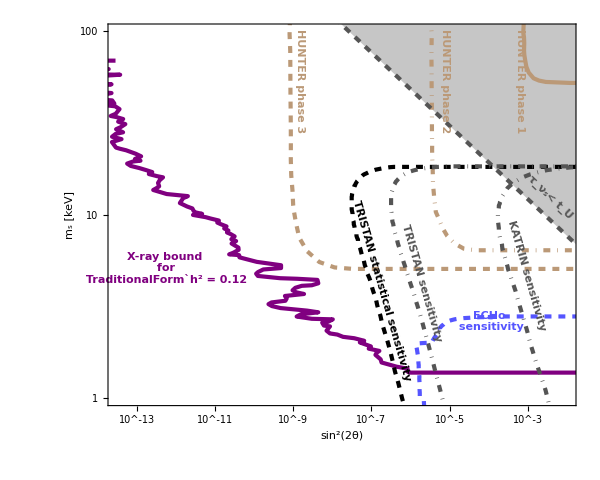

```mathematica
Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times New Roman"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8,(* PlotLabel->Row[{
"Experimental sensitivities"}],*)
Prolog->expsensitivity012,
Epilog->epilogue012,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

### Dataset for plots

#### get relic abundance lines with 100 % DM fraction

```mathematica
getabundance100 = Function[{mϕ,ϵ},
Block[{},
filestring[vals__]:= ToString@StringForm["omegadm_pseudoscalar_``_``.dat",vals];
omegadm100[mϕ,ϵ] = Import[NotebookDirectory[]<>"/data/abundance012/" <>filestring[mϕ,ϵ], "Table"]
]];
```

```mathematica
epsilon = Join[Table[i,{i,0.1,0.9,0.1}],Table[i,{i,1,9,1}],Table[i,{i,10,100,1}]];
getabundance100[10,0];
getabundance100[10,#]&/@ epsilon;
getabundance100[50,#]&/@ epsilon;
getabundance100[100,#]&/@ epsilon;
```

#### get relic abundance lines with 10% DM fraction

```mathematica
getabundance10 = Function[{mϕ,ϵ},
Block[{},
filestring[vals__]:= ToString@StringForm["omegadm_pseudoscalar_``_``.dat",vals];
omegadm10[mϕ,ϵ] = Import[NotebookDirectory[]<>"/data/abundance0012/" <>filestring[mϕ,ϵ], "Table"]
]];
```

```mathematica
getabundance10[10,0];
```

```mathematica
getabundance10[10,#]&/@ epsilon;
getabundance10[50,#]&/@ epsilon;
getabundance10[100,#]&/@ epsilon;
```

#### get (r.b2f)_DW lines

```mathematica
getdistfn = Function[{mϕ,ϵ},
Block[{},
filestring[vals__]:= ToString@StringForm["r2f_pseudoscalar_``_``.dat",vals];
r2f[mϕ,ϵ] = Import[NotebookDirectory[]<>"/data/distribution_function/" <>filestring[mϕ,ϵ], "Table"]
]];
```

```mathematica
epsilon = Join[Table[i,{i,0.1,0.9,0.01}],Table[i,{i,1,9,.1}],Table[i,{i,10,100,1}]];
getdistfn[10,0];
getdistfn[10,#]&/@epsilon;
getdistfn[50,#]&/@ epsilon;
getdistfn[100,#]&/@ epsilon;
```

#### get df/dT lines

```mathematica
getdffn = Function[{mϕ,ϵ},
Block[{},
filestring[vals__]:= ToString@StringForm["df_pseudoscalar_``_``.dat",vals];
df[mϕ,ϵ] = Import[NotebookDirectory[]<>"/data/rhs/" <>filestring[mϕ,ϵ], "Table"]
]];
```

```mathematica
epsilon = Join[Table[i,{i,0.1,0.9,0.01}],Table[i,{i,1,9,.1}],Table[i,{i,10,100,1}]];
```

```mathematica
getdffn[10,0];
getdffn[10,#]&/@epsilon;
getdffn[50,#]&/@ epsilon;
getdffn[100,#]&/@ epsilon;
```

#### free streaming length as a function of ϵ

BP1: {7.1 keV, 5 × 10^-11}

```mathematica
lambdabp110=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_7.1_10.dat", "Table"];
lambdabp150=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_7.1_50.dat", "Table"];
lambdabp1100=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_7.1_100.dat", "Table"];
```

BP2: {10 keV, 1.1 × 10^-9}

```mathematica
lambdabp210=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_10_10.dat", "Table"];
lambdabp250=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_10_50.dat", "Table"];
lambdabp2100=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_10_100.dat", "Table"];
```

BP3: {30 keV, 1.1 × 10^-11}

```mathematica
lambdabp310=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_30_10.dat", "Table"];
lambdabp350=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_30_50.dat", "Table"];
lambdabp3100=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_30_100.dat", "Table"];
```

BP4: {50 keV, 1.1 × 10^-11}

```mathematica
lambdabp410=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_50_10.dat", "Table"];
lambdabp450=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_50_50.dat", "Table"];
lambdabp4100=Import[NotebookDirectory[]<>"/data/freestreaming_length/lfs_pseudoscalar_50_100.dat", "Table"];
```

### Differential production rate for m_ϕ = 10GeV

```mathematica
df0 = {Black,Thick,Thickness[0.005],Line[df[10,0]]};
df1 = {Hue[0,#,1],Thick,Thickness[0.004],Line[df[10,#]]}&/@ Table[i,{i,0.1,0.9,0.01}];
df2 = {Hue[0.3,#/10,1],Thick,Thickness[0.004],Line[df[10,#]]}&/@ Table[i,{i,1,9,.1}];
df3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[df[10,#]]}&/@ Table[i,{i,10,100,1}];
df4 = {Black,Dashed,Thickness[0.005],Line[df[10,13]]};
```

```mathematica
dflines = Join[df2,df1,df3,df0,df4];
```

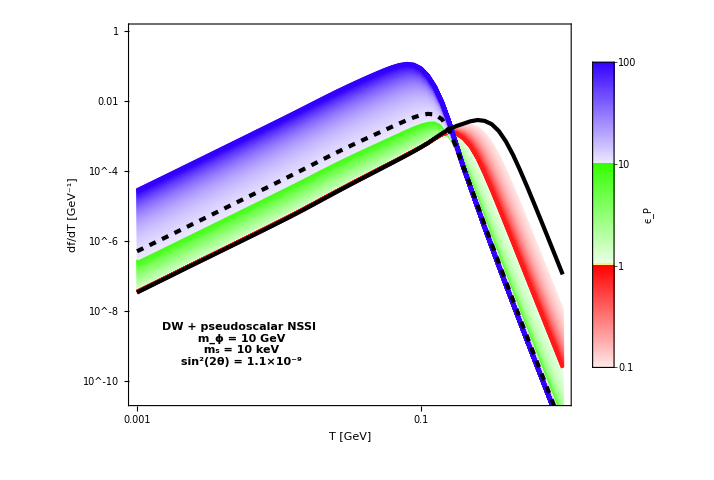

```mathematica
dfDM = Plot[{},{x,-3,1},PlotRange->{{-3,0},{-10.5,-0.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["T [GeV]"],SingleLetterItalics->True,26,Black,FontFamily->"Times"],Style[HoldForm["df/dT [GeV^-1]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8,(*PlotLabel->Row[{
"DW + pseudoscalar NSSI distribution functions"}],*)
Prolog->dflines,
Epilog->{
FontSize ->18,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 10 GeV\n m_s = 10 keV\n sin^2(2θ) = 1.1×10^-9"],Bold],-0 Degree],Scaled[{0.25,0.16}]]},


FrameTicks->{{fticksy,fticksy0},{fticksx,fticksx0}},PlotLegends->Placed[barlegend,Right]]
```

```mathematica
Export[NotebookDirectory[]<>"plots/dfVsT_pseudoscalar_10.pdf",dfDM]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/dfVsT_pseudoscalar_10.pdf

### Differential production rate for m_ϕ = 50GeV

```mathematica
df0 = {Black,Thick,Thickness[0.005],Line[df[10,0]]};
df1 = {Hue[0,#,1],Thick,Thickness[0.004],Line[df[50,#]]}&/@ Table[i,{i,0.1,0.9,0.01}];
df2 = {Hue[0.3,#/10,1],Thick,Thickness[0.004],Line[df[50,#]]}&/@ Table[i,{i,1,9,.1}];
df3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[df[50,#]]}&/@ Table[i,{i,10,100,1}];
df4 = {Black,Dashed,Thickness[0.005],Line[df[50,4.]]};
df5 = {Black,Dashed,Thickness[0.005],Line[df[50,0.2]]};
dflines = Join[df2,df1,df3,df0,df4,df5];
```

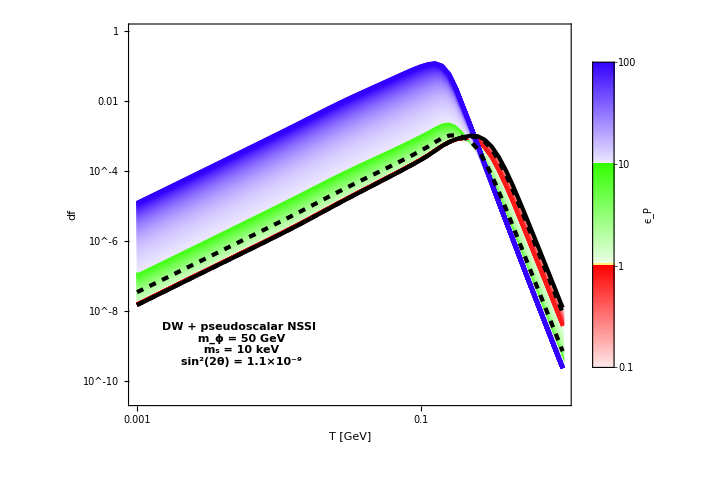

```mathematica
dfDM = Plot[{},{x,-3,1},PlotRange->{{-3,0},{-10.5,-0.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["T [GeV]"],26,Black,FontFamily->"Times"],Style[HoldForm["df/dT [GeV^-1]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, (*PlotLabel->Row[{
"DW + pseudoscalar NSSI distribution functions"}],*)
Prolog->dflines,
Epilog->{
FontSize ->18,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 50 GeV\n m_s = 10 keV\n sin^2(2θ) = 1.1×10^-9"],Bold],-0 Degree],Scaled[{0.25,0.16}]]},

FrameTicks->{{fticksy,fticksy0},{fticksx,fticksx0}},PlotLegends->Placed[barlegend,Right]]
```

```mathematica
Export[NotebookDirectory[]<>"plots/dfVsT_pseudoscalar_50.pdf",dfDM]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/dfVsT_pseudoscalar_50.pdf

### Differential production rate for m_ϕ = 100GeV

```mathematica
df0 = {Black,Thick,Thickness[0.005],Line[df[10,0]]};
df1 = {Hue[0,#,1],Thick,Thickness[0.004],Line[df[100,#]]}&/@ Table[i,{i,0.1,0.9,0.01}];
df2 = {Hue[0.3,#/10,1],Thick,Thickness[0.004],Line[df[100,#]]}&/@ Table[i,{i,1,9,.1}];
df3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[df[100,#]]}&/@ Table[i,{i,10,100,1}];
df4 = {Black,Dashed,Thickness[0.005],Line[df[10,0]]};
```

```mathematica
dflines = Join[df2,df1,df3,df0,df4];
```

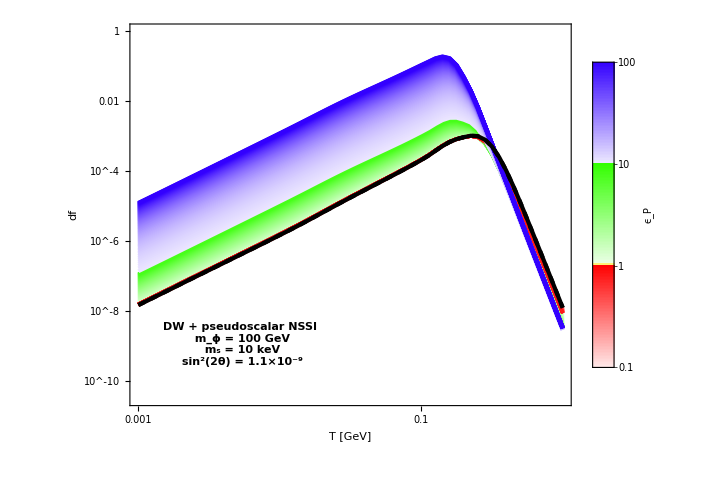

```mathematica
dfDM = Plot[{},{x,-3,1},PlotRange->{{-3,0},{-10.5,-0.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["T [GeV]"],26,Black,FontFamily->"Times"],Style[HoldForm["df/dT [GeV^-1]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, (*PlotLabel->Row[{
"DW + pseudoscalar NSSI distribution functions"}],*)
Prolog->dflines,
Epilog->{
FontSize ->18,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 100 GeV\n m_s = 10 keV\n sin^2(2θ) = 1.1×10^-9"],Bold],-0 Degree],Scaled[{0.25,0.16}]]},

FrameTicks->{{fticksy,fticksy0},{fticksx,fticksx0}},PlotLegends->Placed[barlegend,Right]]
```

```mathematica
Export[NotebookDirectory[]<>"plots/dfVsT_pseudoscalar_100.pdf",dfDM]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/dfVsT_pseudoscalar_100.pdf

### Distribution functions for m_ϕ = 10GeV

```mathematica
r2f0 = {Black,Thick,Thickness[0.004],Line[r2f[10,0]]};
r2f1 = {Hue[0,#,1,#/2],Thick,Thickness[0.004],Line[r2f[10,#]]}&/@ Table[i,{i,0.1,0.9,0.01}];
r2f2 = {Hue[0.3,#/10,1,#/20],Thick,Thickness[0.004],Line[r2f[10,#]]}&/@ Table[i,{i,1,9,.1}];
r2f3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[r2f[10,#]]}&/@ Table[i,{i,10,100,1}];
r2f4 = {Black,Dashed,Thickness[0.005],Line[r2f[10,13]]};
```

```mathematica
r2flines = Join[r2f2,r2f1,r2f3,r2f0,r2f4];
```

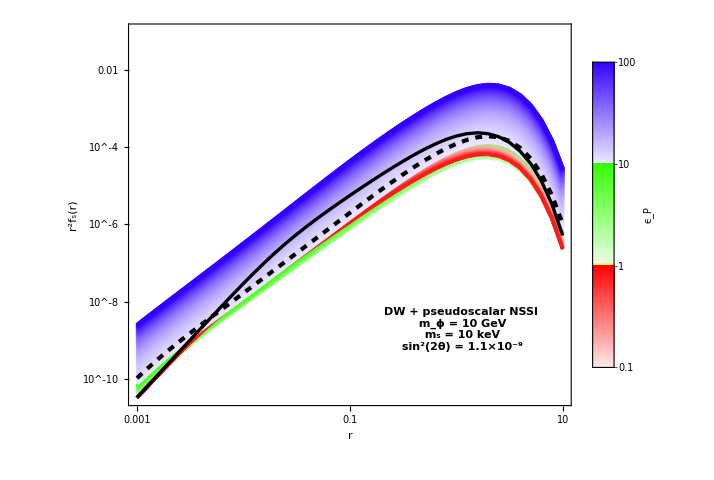

```mathematica
r2fDM = Plot[{},{x,-3,1},PlotRange->{{-3, 1},{-10.5,-1.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm[r],26,Black,FontFamily->"Times"],Style[HoldForm["r^2f_s(r)"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8,(* PlotLabel->Row[{
"DW + pseudoscalar NSSI distribution functions"}],*)
Prolog->r2flines,
Epilog->{
FontSize ->20,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 10 GeV\n m_s = 10 keV\n sin^2(2θ) = 1.1×10^-9"],Bold],-0 Degree],Scaled[{0.75,0.2}]]},

FrameTicks->{{fticksy,fticksy0},{fticksx,fticksx0}},PlotLegends->Placed[barlegend,Right]]
```

```mathematica
Export[NotebookDirectory[]<>"plots/r2f_pseudoscalar_10.pdf",r2fDM]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/r2f_pseudoscalar_10.pdf

### Distribution functions for m_ϕ = 50GeV

```mathematica
r2f0 = {Black,Thick,Thickness[0.004],Line[r2f[10,0]]};
r2f1 = {Hue[0,#,1,#],Thick,Thickness[0.004],Line[r2f[50,#]]}&/@ Table[i,{i,0.1,0.9,0.01}];
r2f2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.004],Line[r2f[50,#]]}&/@ Table[i,{i,1,9,.1}];
r2f3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[r2f[50,#]]}&/@ Table[i,{i,10,100,1}];
r2f4 = {Black,Dashed,Thickness[0.005],Line[r2f[50,4.]]};
r2f5 = {Black,Dashed,Thickness[0.005],Line[r2f[50,0.2]]};
r2flines = Join[r2f2,r2f3,r2f1,r2f0,r2f4,r2f5];
```

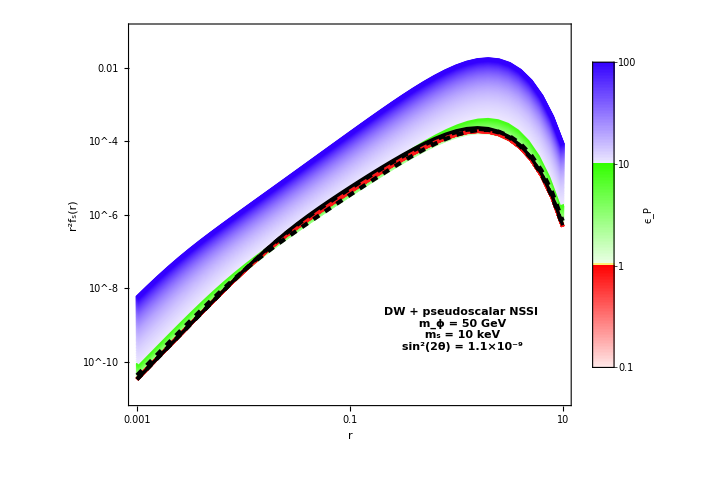

```mathematica
r2fDM = Plot[{},{x,-3,1},PlotRange->{{-3, 1},{-11,-1.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm[r],26,Black,FontFamily->"Times"],Style[HoldForm["r^2f_s(r)"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8,(* PlotLabel->Row[{
"DW + pseudoscalar NSSI distribution functions"}],*)
Prolog->r2flines,
Epilog->{
FontSize ->20,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 50 GeV\n m_s = 10 keV\n sin^2(2θ) = 1.1×10^-9"],Bold],-0 Degree],Scaled[{0.75,0.2}]]},
FrameTicks->{{fticksy,fticksy0},{fticksx,fticksx0}},PlotLegends->Placed[barlegend,Right]]
```

```mathematica
Export[NotebookDirectory[]<>"plots/r2f_pseudoscalar_50.pdf",r2fDM]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/r2f_pseudoscalar_50.pdf

### Distribution functions for m_ϕ = 100GeV

```mathematica
r2f0 = {Black,Thick,Thickness[0.004],Line[r2f[10,0]]};
r2f1 = {Hue[0,#,1],Thick,Thickness[0.004],Line[r2f[100,#]]}&/@ Table[i,{i,0.1,0.9,0.01}];
r2f2 = {Hue[0.3,#/10,1],Thick,Thickness[0.004],Line[r2f[100,#]]}&/@ Table[i,{i,1,9,.1}];
r2f3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[r2f[100,#]]}&/@ Table[i,{i,10,100,1}];
r2f4 = {Black,Dashed,Thickness[0.004],Line[r2f[10,0]]};
```

```mathematica
r2flines = Join[r2f2,r2f3,r2f1,r2f0,r2f4];
```

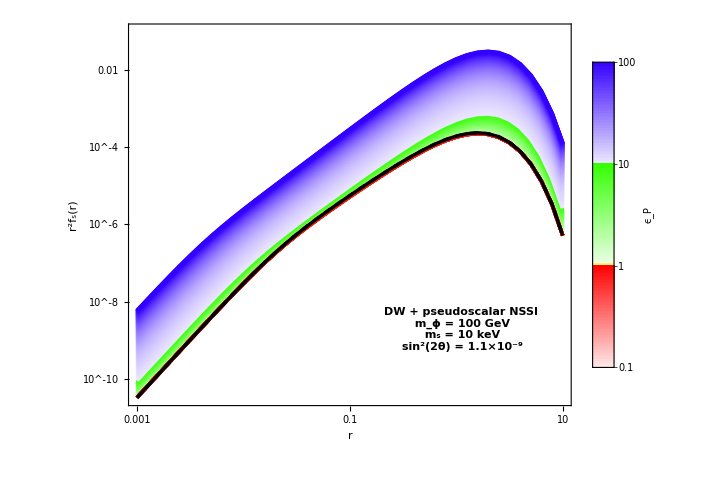

```mathematica
r2fDM = Plot[{},{x,-3,1},PlotRange->{{-3, 1},{-10.5,-1.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm[r],26,Black,FontFamily->"Times"],Style[HoldForm["r^2f_s(r)"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, (* PlotLabel->Row[{
"DW + pseudoscalar NSSI distribution functions"}],*)
Prolog->r2flines,
Epilog->{
FontSize ->20,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 100 GeV\n m_s = 10 keV\n sin^2(2θ) = 1.1×10^-9"],Bold],-0 Degree],Scaled[{0.75,0.2}]]},

FrameTicks->{{fticksy,fticksy0},{fticksx,fticksx0}},PlotLegends->Placed[barlegend,Right]]
```

```mathematica
Export[NotebookDirectory[]<>"plots/r2f_pseudoscalar_100.pdf",r2fDM]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/r2f_pseudoscalar_100.pdf

### Parameter space for m_ϕ = 10GeV with 100% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm100[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm100[10,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.006],Line[omegadm100[10,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[omegadm100[10,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity012];
```

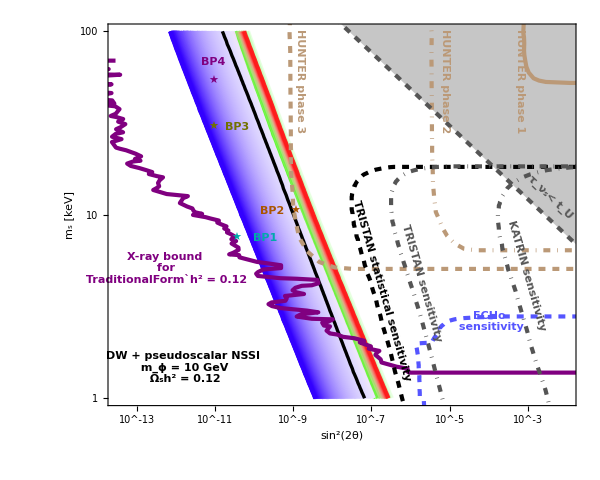

```mathematica
epilogue10 = Join[epilogue012,{FontSize->24,Darker[Cyan],Text[Rotate["★",-0 Degree],Scaled[{0.275,0.44}]],FontSize->18,Darker[Cyan],Text[Rotate[Style["BP1",Bold],-0 Degree],Scaled[{0.335,0.44}]],FontSize->24,Darker[Orange],Text[Rotate["★",-0 Degree],Scaled[{0.4,0.51}]],FontSize->18,Darker[Orange],Text[Rotate[Style["BP2",Bold],-0 Degree],Scaled[{0.35,0.51}]],FontSize->24,Darker[Darker[Yellow]],Text[Rotate["★",-0 Degree],Scaled[{0.225,0.73}]],FontSize->18,Darker[Darker[Yellow]],Text[Rotate[Style["BP3",Bold],-0 Degree],Scaled[{0.275,0.73}]],
FontSize->24,Purple,Text[Rotate["★",-0 Degree],Scaled[{0.225,0.85}]],FontSize->18,Purple,Text[Rotate[Style["BP4",Bold],-0 Degree],Scaled[{0.225,0.9}]]},
{FontSize ->14,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 10 GeV\n Ω_sh^2 = 0.12"],Bold],-0 Degree],Scaled[{0.16,0.1}]]}];parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_pseudoscalar_10_012.pdf",parameterspace]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/parameter_space_pseudoscalar_10_012.pdf

### Parameter space for m_ϕ = 50GeV with 100% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm100[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm100[50,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.006],Line[omegadm100[50,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[omegadm100[50,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity012];
```

```mathematica
epilogue10 = Join[epilogue012,{FontSize->24,Darker[Cyan],Text[Rotate["★",-0 Degree],Scaled[{0.275,0.44}]],FontSize->18,Darker[Cyan],Text[Rotate[Style["BP1",Bold],-0 Degree],Scaled[{0.325,0.44}]],FontSize->24,Darker[Orange],Text[Rotate["★",-0 Degree],Scaled[{0.4,0.51}]],FontSize->18,Darker[Orange],Text[Rotate[Style["BP2",Bold],-0 Degree],Scaled[{0.45,0.51}]],FontSize->24,Darker[Darker[Yellow]],Text[Rotate["★",-0 Degree],Scaled[{0.225,0.73}]],FontSize->18,Darker[Darker[Yellow]],Text[Rotate[Style["BP3",Bold],-0 Degree],Scaled[{0.225,0.77}]],
FontSize->24,Purple,Text[Rotate["★",-0 Degree],Scaled[{0.225,0.85}]],FontSize->18,Purple,Text[Rotate[Style["BP4",Bold],-0 Degree],Scaled[{0.225,0.9}]]},
{FontSize ->14,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 50 GeV\n Ω_sh^2 = 0.12"],Bold],-0 Degree],Scaled[{0.16,0.1}]]}];
```

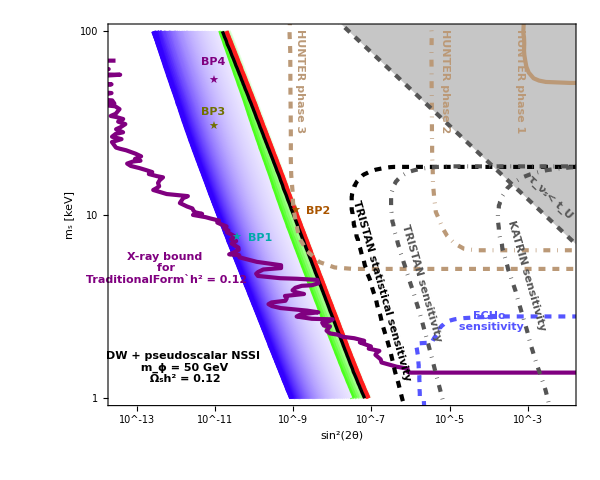

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_pseudoscalar_50_012.pdf",parameterspace]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/parameter_space_pseudoscalar_50_012.pdf

### Parameter space for m_ϕ = 100GeV with 100% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm100[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm100[100,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.007],Line[omegadm100[100,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[omegadm100[100,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity012];
```

```mathematica
epilogue10 = Join[epilogue012,{FontSize->24,Darker[Cyan],Text[Rotate["★",-0 Degree],Scaled[{0.275,0.44}]],FontSize->18,Darker[Cyan],Text[Rotate[Style["BP1",Bold],-0 Degree],Scaled[{0.325,0.44}]],FontSize->24,Darker[Orange],Text[Rotate["★",-0 Degree],Scaled[{0.4,0.51}]],FontSize->18,Darker[Orange],Text[Rotate[Style["BP2",Bold],-0 Degree],Scaled[{0.45,0.51}]],FontSize->24,Darker[Darker[Yellow]],Text[Rotate["★",-0 Degree],Scaled[{0.225,0.73}]],FontSize->18,Darker[Darker[Yellow]],Text[Rotate[Style["BP3",Bold],-0 Degree],Scaled[{0.225,0.77}]],
FontSize->24,Purple,Text[Rotate["★",-0 Degree],Scaled[{0.225,0.85}]],FontSize->18,Purple,Text[Rotate[Style["BP4",Bold],-0 Degree],Scaled[{0.225,0.9}]]},
{FontSize ->14,
Black, Text[Rotate[Style[Framed["DW + pseudoscalar NSSI\n m_ϕ = 100 GeV\n Ω_sh^2 = 0.12"],Bold],-0 Degree],Scaled[{0.16,0.1}]]}];
```

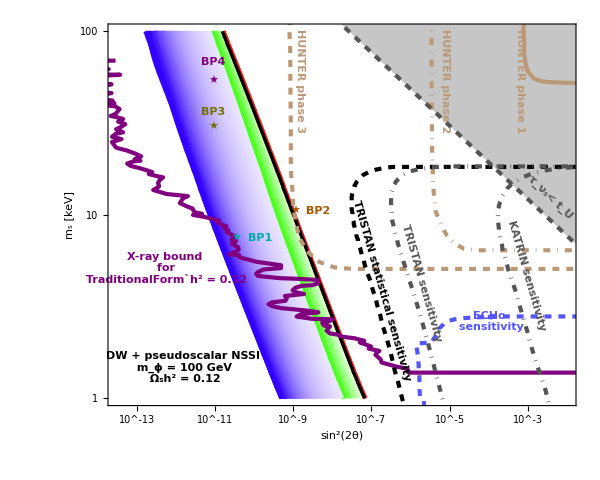

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}}]
```

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_pseudoscalar_100_012.pdf",parameterspace]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/parameter_space_pseudoscalar_100_012.pdf

### Parameter space for m_ϕ = 10GeV with 10% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm10[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm10[10,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.0065],Line[omegadm10[10,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.005],Line[omegadm10[10,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity0012];
```

```mathematica
epilogue10 = Join[epilogue0012,{FontSize->24,Darker[Cyan],Text[Rotate["★",-0 Degree],Scaled[{0.275,0.44}]],FontSize->18,Darker[Cyan],Text[Rotate[Style["BP1",Bold],-0 Degree],Scaled[{0.3,0.4}]],FontSize->24,Darker[Orange],Text[Rotate["★",-0 Degree],Scaled[{0.4,0.51}]],FontSize->18,Darker[Orange],Text[Rotate[Style["BP2",Bold],-0 Degree],Scaled[{0.45,0.51}]],FontSize->24,Darker[Darker[Yellow]],Text[Rotate["★",-0 Degree],Scaled[{0.225,0.73}]],FontSize->18,Darker[Darker[Yellow]],Text[Rotate[Style["BP3",Bold],-0 Degree],Scaled[{0.275,0.73}]],
FontSize->24,Purple,Text[Rotate["★",-0 Degree],Scaled[{0.225,0.85}]],FontSize->18,Purple,Text[Rotate[Style["BP4",Bold],-0 Degree],Scaled[{0.275,0.85}]]},
{FontSize->15,
Lighter[Purple], Text[Rotate[Style["X-ray bound\n for\n TraditionalForm`h^2 = 0.012", Bold],-0 Degree],Scaled[{0.1,0.43}]], 
FontSize ->14,
Black, Text[Rotate[Style[Framed["m_ϕ = 10 GeV\n Ω_sh^2 = 0.012"],Bold],-0 Degree],Scaled[{0.12,0.1}]]}];
```

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}},PlotLegends->Placed[barlegend,Right]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_pseudoscalar_10_0012.pdf",parameterspace]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/parameter_space_pseudoscalar_10_0012.pdf

### Parameter space for m_ϕ = 50GeV with 10% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm10[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm10[50,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.006],Line[omegadm10[50,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.006],Line[omegadm10[50,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity0012];
```

```mathematica
epilogue10 = Join[epilogue0012,{FontSize->24,Darker[Cyan],Text[Rotate["★",-0 Degree],Scaled[{0.275,0.44}]],FontSize->18,Darker[Cyan],Text[Rotate[Style["BP1",Bold],-0 Degree],Scaled[{0.275,0.4}]],FontSize->24,Darker[Orange],Text[Rotate["★",-0 Degree],Scaled[{0.4,0.51}]],FontSize->18,Darker[Orange],Text[Rotate[Style["BP2",Bold],-0 Degree],Scaled[{0.45,0.51}]],FontSize->24,Darker[Darker[Yellow]],Text[Rotate["★",-0 Degree],Scaled[{0.225,0.73}]],FontSize->18,Darker[Darker[Yellow]],Text[Rotate[Style["BP3",Bold],-0 Degree],Scaled[{0.275,0.73}]],
FontSize->24,Purple,Text[Rotate["★",-0 Degree],Scaled[{0.225,0.85}]],FontSize->18,Purple,Text[Rotate[Style["BP4",Bold],-0 Degree],Scaled[{0.275,0.85}]]},
{FontSize->13,
Lighter[Purple], Text[Rotate[Style["X-ray bound\n for\n TraditionalForm`h^2 = 0.012", Bold],-0 Degree],Scaled[{0.5,0.18}]], 
FontSize ->14,
Black, Text[Rotate[Style[Framed["m_ϕ = 50 GeV\n Ω_sh^2 = 0.012"],Bold],-0 Degree],Scaled[{0.12,0.1}]]}];
```

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}},PlotLegends->Placed[barlegend,Right]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_pseudoscalar_50_0012.pdf",parameterspace]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/parameter_space_pseudoscalar_50_0012.pdf

### Parameter space for m_ϕ = 100GeV with 10% DM fraction

```mathematica
line0 = {Black,Thick,Thickness[0.004],Line[omegadm10[10,0]]};
line1 = {Hue[0,#,1,#],Thick,Thickness[0.005],Line[omegadm10[100,#]]}&/@ Table[i,{i,0.1,0.9,0.1}];
line2 = {Hue[0.3,#/10,1,#/10],Thick,Thickness[0.0065],Line[omegadm10[100,#]]}&/@ Table[i,{i,1,9,1}];
line3 = {Hue[0.7,#/100,1],Thick,Thickness[0.006],Line[omegadm10[100,#]]}&/@ Table[i,{i,10,100,1}];
```

```mathematica
paramspacelines = Join[line2,line3,line1,line0];
```

```mathematica
prologue10 = Join[paramspacelines,expsensitivity0012];
```

```mathematica
epilogue10 = Join[epilogue0012,{FontSize->24,Darker[Cyan],Text[Rotate["★",-0 Degree],Scaled[{0.275,0.44}]],FontSize->18,Darker[Cyan],Text[Rotate[Style["BP1",Bold],-0 Degree],Scaled[{0.225,0.44}]],FontSize->24,Darker[Orange],Text[Rotate["★",-0 Degree],Scaled[{0.4,0.51}]],FontSize->18,Darker[Orange],Text[Rotate[Style["BP2",Bold],-0 Degree],Scaled[{0.45,0.51}]],FontSize->24,Darker[Darker[Yellow]],Text[Rotate["★",-0 Degree],Scaled[{0.225,0.73}]],FontSize->18,Darker[Darker[Yellow]],Text[Rotate[Style["BP3",Bold],-0 Degree],Scaled[{0.275,0.73}]],
FontSize->24,Purple,Text[Rotate["★",-0 Degree],Scaled[{0.225,0.85}]],FontSize->18,Purple,Text[Rotate[Style["BP4",Bold],-0 Degree],Scaled[{0.275,0.85}]]},
{FontSize->13,
Lighter[Purple], Text[Rotate[Style["X-ray bound\n for\n TraditionalForm`h^2 = 0.012", Bold],-0 Degree],Scaled[{0.5,0.18}]], 
FontSize ->14,
Black, Text[Rotate[Style[Framed["m_ϕ = 100 GeV\n Ω_sh^2 = 0.012"],Bold],-0 Degree],Scaled[{0.12,0.1}]]}];
```

```mathematica
parameterspace = Plot[{},{x,-16,-3},PlotRange->{{-13.5, -2},{0, 2.}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style[HoldForm["sin^2(2θ)"],26,Black,FontFamily->"Times"],Style[HoldForm["m_s [keV]"],26,Black,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8, 
Prolog->prologue10,
Epilog->epilogue10,
FrameTicks->{{ticksy,ticksy0},{ticksx,ticksx0}},PlotLegends->Placed[barlegend,Right]]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"plots/parameter_space_pseudoscalar_100_0012.pdf",parameterspace]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/parameter_space_pseudoscalar_100_0012.pdf

### Free streaming length

```mathematica
lambdahot={{-1,-1},{2,-1},{2,2},{-1,2}};
lambdacold={{-1,-2},{2,-2},{2,-3},{-1,-3}};
```

```mathematica
pointslegend={Style["BP1: m_s = 7.1 keV , sin^2(2θ) = 5×10^-11\n",Bold,Darker[Cyan]],Style["BP2: m_s = 10 keV , sin^2(2θ) = 1.1×10^-9\n",Bold,Darker[Orange]],Style[" BP3: m_s = 30 keV , sin^2(2θ) = 1.1×10^-11\n",Bold,Darker[Darker[Yellow]]],Style[" BP4: m_s = 50 keV , sin^2(2θ) = 1.1×10^-11",Bold,Purple]};
masslegend={Style["DW + pseudoscalar NSSI\n",Bold,Black],Style[" m_ϕ = 10 GeV   ",Bold,Black],Graphics[{Thick,Thickness[0.03],Line[{{0,0},{1,0}}]},ImageSize->60,AspectRatio->1/20],Style["\n m_ϕ = 50 GeV   ",Bold,Black],Graphics[{Dashed,Thickness[0.03],Line[{{0,0},{1,0}}]},ImageSize->60,AspectRatio->1/20],Style["\n m_ϕ = 100 GeV ",Bold,Black],Graphics[{Dotted,Thickness[0.03],Line[{{0,0},{1,0}}]},ImageSize->60,AspectRatio->1/20]};
abundancelegend={Style[" ▲  Ω_sh.b2 = 0.012  \n",Bold],Style[" ◼  Ω_sh.b2 = 0.12    ",Bold]};
```

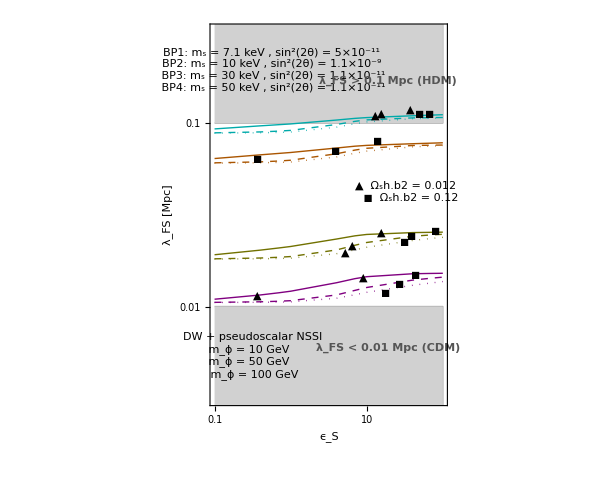

```mathematica
lfs=Plot[{},{x,-1,2},PlotRange->{{-1,2},{-2.5,-0.5}},
Frame->True,BaseStyle->{ FontFamily->"Times",FontSize->20},
FrameLabel->{Style["ϵ_S",26,Black,FontSlant->Italic,SingleLetterItalics->True, FontFamily->"Times"],Style[HoldForm[ "λ_FS [Mpc]"],Black,26,FontFamily->"Times"]},FrameStyle->Directive[FontSize->20],
ImageMargins->3,FrameTicksStyle->Black,
ImageSize->600,Axes->False,AspectRatio->0.8,
Prolog->{Lighter[Gray],Line[lambdahot],GrayLevel[0.82],Polygon[lambdahot],Lighter[Gray],Line[lambdacold],GrayLevel[0.82],Polygon[lambdacold],Darker[Orange],Thick,Line[lambdabp210],Purple,Thick,Line[lambdabp410],Darker[Cyan],Thick,Line[lambdabp110],Darker[Darker[Yellow]],Thick,Line[lambdabp310],Darker[Orange],Dashed,Line[lambdabp250],Darker[Orange],Dotted,Line[lambdabp2100],Purple,Dashed,Line[lambdabp450],Purple,Dotted,Line[lambdabp4100],Darker[Cyan],Dashed,Line[lambdabp150],Darker[Cyan],Dotted,Line[lambdabp1100],Darker[Darker[Yellow]],Dashed,Line[lambdabp350],Darker[Darker[Yellow]],Dotted,Line[lambdabp3100]
},
Epilog->{
FontSize ->14,
Black, Text[Rotate[Framed@Apply[StringJoin,ToString[#,StandardForm]&/@pointslegend],-0 Degree],Scaled[{0.26,0.88}]],
FontSize ->12,
Black, Text[Rotate[Framed@Apply[StringJoin,ToString[#,StandardForm]&/@masslegend],-0 Degree],Scaled[{0.18,0.13}]],
FontSize ->18,
Black, Text[Rotate[Framed@Apply[StringJoin,ToString[#,StandardForm]&/@abundancelegend],-0 Degree],Scaled[{0.84,0.56}]],FontSize ->22,Darker[Gray],Text[Rotate[Style["λ_FS > 0.1 Mpc (HDM)",Bold],0 Degree],Scaled[{0.75,0.85}]],
FontSize ->22,Darker[Gray],Text[Rotate[Style["λ_FS < 0.01 Mpc (CDM)",Bold],0 Degree],Scaled[{0.75,0.15}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.865,0.342}]],
FontSize->18,Darker[Black],Text[Rotate["▲",-0 Degree],Scaled[{0.845,0.775}]],
FontSize->18,Darker[Black],Text[Rotate["▲",-0 Degree],Scaled[{0.72,0.765}]],
FontSize->18,Darker[Black],Text[Rotate["▲",-0 Degree],Scaled[{0.695,0.76}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.925,0.765}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.885,0.763}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.705,0.693}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.53,0.666}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.2,0.646}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.8,0.318}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.74,0.295}]],
FontSize->18,Darker[Black],Text[Rotate["▲",-0 Degree],Scaled[{0.72,0.452}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.95,0.458}]],
FontSize->18,Darker[Black],Text[Rotate["▲",-0 Degree],Scaled[{0.2,0.288}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.85,0.445}]],
FontSize->18,Darker[Black],Text[Rotate["▲",-0 Degree],Scaled[{0.6,0.42}]],
FontSize->18,Darker[Black],Text[Rotate["▲",-0 Degree],Scaled[{0.57,0.402}]],
FontSize->18,Darker[Black],Text[Rotate["◼",-0 Degree],Scaled[{0.82,0.428}]],
FontSize->18,Darker[Black],Text[Rotate["▲",-0 Degree],Scaled[{0.645,0.335}]]
},

FrameTicks->{{lticksy,fticksy0},{fticksx,fticksx0}}]
```

```mathematica
Export[NotebookDirectory[]<>"plots/lfs_pseudoscalar.pdf",lfs]
```

C:\Users\Aaroodd\Documents\NSI-sterile-neutrino\Active neutrino NSI\DW with Pseudocalar NSI\plots/lfs_pseudoscalar.pdf